## Problem 1.17d

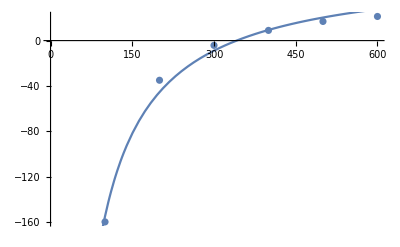

```mathematica
temp={100,200,300,400,500,600};
B={-160,-35,-4.2,9,16.9,21.3};
data=Thread[{temp,B}];
R=8.315;
nlm=NonlinearModelFit[data,b-a/(R T),{b,a},T];
Show[ListPlot[data],Plot[nlm[x],{x,50,600}]]
```

```mathematica
2*9.8*28.74/(7*6.022*1.381)
```

9.67632